```mathematica
Needs["HypothesisTesting`"]
```

10

883.85

26.6512

6.0307

{864.785,902.915}

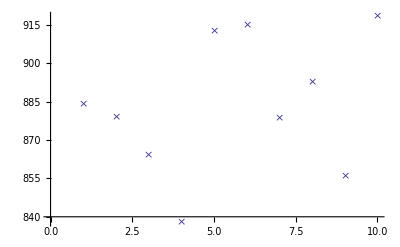

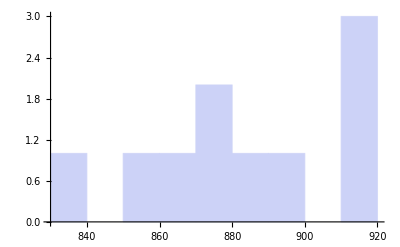

-Graphics3D-

```mathematica
B={
884.2,
879,
864,
838,
912.5,
915.0,
878.7,
892.8,
855.9,
918.4
};
Length[B]
m=Mean[B]//N
sd=StandardDeviation[B]//N
2sd/m*100
MeanCI[B,ConfidenceLevel->.95]
ListPlot[B,PlotMarkers-> {"×",Large}]
Histogram[B,9]
Plot3D[Likelihood[NormalDistribution[μ,σ],B],{μ, 850,900},{σ,1,40},PlotRange->All]
```